```mathematica
5+3
```

```mathematica
8
```

```mathematica
(*expression*)
(*head[agr1, agr2, ..., agrN]*)
```

```mathematica
a+b/.b -> x+b/y
```

a+x+b/y

```mathematica
(* ->  /.  //.*)
```

```mathematica
(a+b)^2/.(a+b)^2->(a^2+2*a*b+b^2)
```

a^2+2 a b+b^2

```mathematica
(*pattern blank*)
(x+y)^2/.(a_+b_)^2->(a^2+2*a*b+b^2)
```

x^2+2 x y+y^2

```mathematica
(a_+b_)^2->(a^2+2*a*b+b^2)
(*(a_+b_)^2*)

(*a_   b_*)
(*(x+y)^2  (_+_)^2*)

(*
regexp;
	.(точка) -- любой символ, который аналог _;
	разница: .-- только 1 символ,
_-- может быть сложнгая конструкция

другим аналогом _ может служить .*
*)
```

(a_+b_)^2→a^2+2 a b+b^2

```mathematica
(x+y+z)^2/.(a_+b_)^2->(a^2+2*a*b+b^2)
```

x^2+2 x (y+z)+(y+z)^2

```mathematica
(x+y+z)^2//.(a_+b_)^2->(a^2+2*a*b+b^2)
```

x^2+y^2+2 y z+z^2+2 x (y+z)

```mathematica
MatchQ[(x+y+z)^2,(a_+b_)^2]
(*выражение (x+y+z)^2 соответствует шаблону (a_+b_)^2*)
```

True

```mathematica
(x+y+z)^2/.(a_+b_)^2->{a,b}
```

{x,y+z}

```mathematica
MatchQ[a,_]
```

True

```mathematica
MatchQ[f[a+123*b_],_ ]
```

True

```mathematica
(*
_ -- простой бланк;
x_ -- именованный бланк, чтобы позже в выражении ссылаться на то, что попалов этот бланк;

_head -- на месте этого бланка может быть ТОЛЬКО выражение с головой head;
*)

MatchQ[{a,b},_List]
```

True

```mathematica
MatchQ[{a,b},{_,_}]
```

True

```mathematica
MatchQ[{a,b},{_}]
```

False

```mathematica
(*конструкция expr1, expr2, ... -- это так называемые последовательности они не удовлетворяют одинарному бланку *)
```

```mathematica
MatchQ[{}, {_}]
```

False

```mathematica
MatchQ[{}, {__}]
```

False

```mathematica
MatchQ[{}, {___}]
```

True

```mathematica
(a_+b_)^2->(a^2+2*a*b+b^2)
(*
1 шаг вычислений с помощью правил и шаблонов 
выражение разбивается, которому применятся замена -> разбирается с помощью шаблона
(стоит слева от стрелкаи), разбирается с целью выяснить, что стоит в место бланков.

2 шаг
в выражение справа от стрелки в место соответствующих букв подлставляется найденные подвыражения для бланков.
*)
```

```mathematica
r1={a_, b__}->{b,a}
```

{a_,b__}→{b,a}

```mathematica
{5,12,9,3,2}/.r1
```

{12,9,3,2,5}

```mathematica
{1,2}/.r1
```

{2,1}

```mathematica
(*
_head;
__head -- все элементы последовательбности должны иметь голову head;
___head 
*)
```

```mathematica
MatchQ[{1,2},{_, __}]
```

True

```mathematica
MatchQ[{1},{_, __}]
```

False

```mathematica
MatchQ[{1},{_, ___}]
```

True

```mathematica
MatchQ[{1,2},{_Integer, __Integer}]
```

True

```mathematica
MatchQ[{1,2, a},{_Integer, __Integer}]
```

False

```mathematica
MatchQ[{1,2, a},{__Integer, __Symbol}]
```

True

```mathematica
MatchQ[123,__]
```

True

```mathematica
MatchQ[123, _?(NumericQ[#]&&(Mod[#,4]==3)&)]
```

True

```mathematica
f[x_]:=x^2
```

```mathematica
f[2]
```

4

```mathematica
f[a]
```

a^2

```mathematica
f1[x_Integer]:=x^2
```

```mathematica
f1[2]
```

4

```mathematica
f1[12.6]
```

f1[12.6]

```mathematica
f2[x_?NumberQ]:=x^2
```

```mathematica
f2[2]
```

4

```mathematica
f2[12.6]
```

158.76

```mathematica
f2[a]
```

f2[a]

```mathematica
(*
два вида ограничений на бланки:
	_head
	и
	_?(предикат)
*)
(*

/; -- ограничение на весь шаблон или на всю подстановку

*)
```

```mathematica
MatchQ[{1,10}, {a_, b_}/;a>b]
```

False

```mathematica
MatchQ[{1,10}, {a_, b_}/;a>b || a==1]
```

True

```mathematica
r2 = {a_, b_,___}:>{b,a}/;(b<a)
(*
-> 
:>

отличатеся так же как и = :=
*)
```

{a_,b_,___}:>{b,a}/;b<a

```mathematica
{10, 2}/.r2
```

{2,10}

```mathematica
l=RandomInteger[{1,10}, 10]
```

{6,5,6,7,5,7,5,3,5,9}

```mathematica
l/.r2
```

{5,6}

```mathematica
r3= {d___, a_, b_,c___}:>{d,b,a, c}/;(b<a)
```

{d___,a_,b_,c___}:>{d,b,a,c}/;b<a

```mathematica
l
```

{6,5,6,7,5,7,5,3,5,9}

```mathematica
l/.r3
```

{5,6,6,7,5,7,5,3,5,9}

```mathematica
l//.r3
```

{3,5,5,5,5,6,6,7,7,9}

```mathematica
a**b
```

a**b

```mathematica
(*
x;
y;
x^3==e;
y^2==e;
y**x**y==y
*)
```

```mathematica
dihRel={NonCommutativeMultiply[a___, e, b___]:>a**b,a___**x**x**x**b___:>a**e**b,a___** y**y**b___:>a**e**b, a___**x**y**x**b___:>a**y**b, NonCommutativeMultiply[a_]:>a}
```

{a___**e**b___:>a**b,a___**x**x**x**b___:>a**e**b,a___**y**y**b___:>a**e**b,a___**x**y**x**b___:>a**y**b,NonCommutativeMultiply[a_]:>a}

```mathematica
x**x**x**x//.dihRel
```

e**x

```mathematica
FullForm[x**x**x]
```

NonCommutativeMultiply[x,x,x]

```mathematica
NonCommutativeMultiply[x,y,x,x,y,x,x,x,y,x,y,x,x]
```

x**y**x**x**y**x**x**x**y**x**y**x**x

```mathematica
w=If[RandomReal[]<.5,x,y];
Do[w=w**If[RandomReal[]<.5,x,y],{i,5}]
w
```

y**y**x**y**x**x

```mathematica
yt = x**x**x**x**y**x
```

x**x**x**x**y**x

```mathematica
yt//.dihRel
```

y

```mathematica
w//.dihRel
```

y**x

```mathematica
a=5
```

5

```mathematica
b:=RandomInteger[{1,10}]
```

```mathematica
{b,b}
```

{1,5}

```mathematica
(*= :=*)
```

```mathematica
g[x_]=x+2
```

2+x

```mathematica
g[2]
```

4

```mathematica
fg[y_]:=y^3
```

```mathematica
fg[a]
```

125

```mathematica
Column[{Row[{"-", "  ",x,"  ", y}], Row[{"1", "  ", x, "  ", y}],Row[{"2", "  ", x, "  ", y}]}]
```

-  x  y
1  x  y
2  x  y

```mathematica
(*
символьные вычисления:

кто задает шаблоны?; (мы/WM)

кто применяет шаблоны?; (мы/WM)

1) задает WM/применяте тоже WM
пример: 1/2 + 1/4 -- преобразуется автоматически
2) задает WM/применяте тоже мы
пример: Simplify[Cos[x]+Sin[x]] -- может упростить, но автоматически не упрощает;
3) задает мы/применяте тоже WM
пример: f[x_]:=x^2 или a=5
4) задает мы/применяте тоже мы
пример: задали rule1 = (x+y)^2/.(a_+b_)^2->(a^2+2*a*b+b^2) применили (x+y)^2/.rule1
*)
```

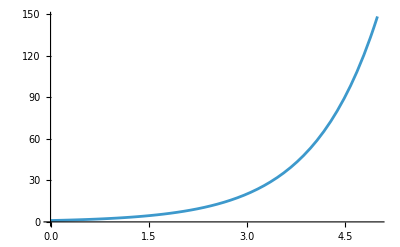

```mathematica
sol=DSolve[y'[x]==y[x],y[x],x];
sol1=sol/. C[1]->1;

Plot[y[x]/. sol1,{x,0,5}]
```